```mathematica
GGrd=ResourceFunction["GeneralizedGridGraph"]
```

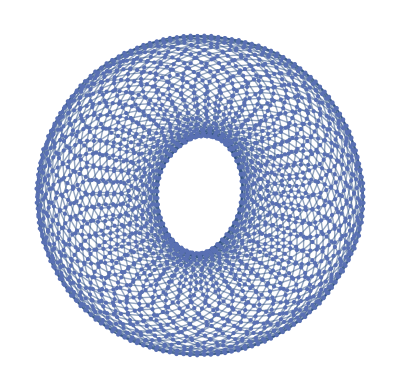

```mathematica
gg1=Graph[GGrd[{50->"Circular",50->"Circular"}]]
```

```mathematica
dists=N@Norm[Min[#,50-#]&/@Abs[QuotientRemainder[1,50]-QuotientRemainder[#,50]]]&/@VertexList[gg1];
```

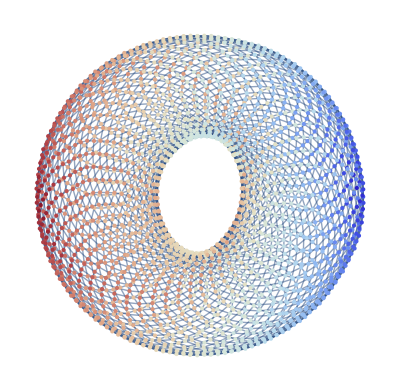

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[gg1,VertexStyle->(#1->#2&@@@Transpose[{VertexList[gg1],ColorData["ThermometerColors"]/@(dists/Max[dists])}])]
```

```mathematica
Abs[QuotientRemainder[96,10]-QuotientRemainder[86,10]]
Abs[QuotientRemainder[96,10]-QuotientRemainder[6,10]]
```

{1,0}

{9,0}

```mathematica
(QuotientRemainder[96,10]-QuotientRemainder[6,10])
```

{9,0}

```mathematica
GridEucDists[g_,v1_]:=Module[{k,p,n},Table[If[v==v1,0,k=GraphDistance[g,1,v];
p=Length@FindPath[g,1,v,{GraphDistance[g,1,v]},Infinity];
n=First@Select[Range[k],Binomial[k,#]==p&];
N@√(n^2+(k-n)^2)],{v,VertexList[g]}]]
```

```mathematica
GridEucDists[gg1,1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

$Aborted

```mathematica
AbsoluteTiming[Max@Abs[EuclideanDistance[emb[[1]],#]&/@emb-GridEucDists[gg1,1]]]
```

$Aborted

```mathematica
k=19
p=19
```

19

19

```mathematica
FindRoot[n!*(k-n)! ==k!/p,{n,k}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n→18.}

```mathematica
NSolve[n!*(k-n)! ==k!/p,n]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[(19-n)! n!==6402373705728000,n]

```mathematica
FindRoot[Binomial[k,n]==p,{n,k}]
```

{n→18.}

```mathematica
FindInstance[Binomial[k,n]==p,n,PositiveIntegers]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[Binomial[19,n]==19,n,]

```mathematica
Integers
```

ℤ

```mathematica
emb[[39]]
```

{2.,19.}

```mathematica
emb[[1]]
```

{1.,1.}